```mathematica
y={-1.48,-1.40, -1.16,-1.08,-1.02,0.14,0.51,0.53,0.078};
```

```mathematica
F[x_,θ_]:=PDF[NormalDistribution[θ,0.1^2]][x]
G[x_]:=PDF[NormalDistribution[0,1]][x]
```

```mathematica
r[x_]:=Evaluate[∫_(-∞)^(+∞) F[x,θ]G[θ]ⅆθ]
```

```mathematica
r[0.14]
```

1.47899×10^-20

```mathematica
post[θ_,x_]:=F[x,θ]G[x]/r[x]
```

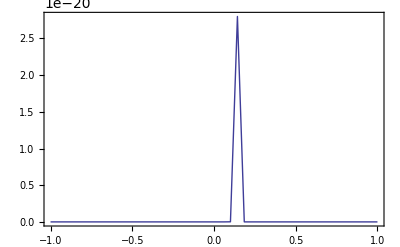

```mathematica
Plot[post[θ,0.14],{θ,-1,1},PlotRange->All,Frame->True]
```

```mathematica
post[θ,x]
```

39.8962 ⅇ^(-0.000049995 x^2-5000. (x-θ)^2)

```mathematica
NormUpdate[θ2_,σ1_,σ2_]:=(ⅇ^(1/2 (-(x-θ)^2/σ1^2-(x-θ2)^2/σ2^2+(x-θ2)^2/(σ1^2+σ2^2))) √(1/σ1^2+1/σ2^2))/(√(2 π))
```

```mathematica
NormUpdate[0,0.1^2,1]
```

39.8962 ⅇ^(1/2 (-0.00009999 x^2-10000. (x-θ)^2))

```mathematica
(PDF[NormalDistribution[θ,σ1]][x]PDF[NormalDistribution[θ2,σ2]][x])/(∫_(-∞)^(+∞) PDF[NormalDistribution[x,σ1]][s]PDF[NormalDistribution[θ2,σ2]][s]ⅆs)
```

ConditionalExpression[(ⅇ^(1/2 (-(x-θ)^2/σ1^2-(x-θ2)^2/σ2^2+(x-θ2)^2/(σ1^2+σ2^2))) √(1/σ1^2+1/σ2^2))/(√(2 π)),Re[1/σ1^2+1/σ2^2]>0]

```mathematica
PDF[NormalDistribution[θ,σ]]
```

Exp[-1/2 ((#1-θ)/σ)^2]/(σ √(2 π))&